# Functions v1 (old)

```mathematica
getCountsBinary[timepoint_,version_]:=Module[
{data}
,
SetDirectory[NotebookDirectory[]];
data=Import["../data/sample_1layers/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[version,10,4]<>".txt","Table"];

Return[{Length[Select[data,#[[4]]=="A"&]],Length[Select[data,#[[4]]=="B"&]],Length[Select[data,#[[4]]=="C"&]]}];
];
```

```mathematica
getAveCountsBinary[timepoint_,versionStart_,versionEnd_]:=Module[
{aves}
,
SetDirectory[NotebookDirectory[]];
aves={0.0,0.0,0.0};
Do[
aves+=getCountsBinary[timepoint,version];
,{version,versionStart,versionEnd}];
aves/=(versionEnd-versionStart+1);

Return[aves];
];
```

# Functions v2

Import a lattice

```mathematica
importLatt[file_]:=Module[
{rl,lattA,lattAsp,lattB,lattBsp,lattC,lattCsp}
,
SetDirectory[NotebookDirectory[]];
rl=ReadList[file,String];

lattA=Map[ToExpression@StringSplit[#][[;;3]]&,Select[rl,StringTake[#,-1]=="A"&]];
lattAsp=SparseArray[Map[#->1&,lattA],{10,10,10},0];

lattB=Map[ToExpression@StringSplit[#][[;;3]]&,Select[rl,StringTake[#,-1]=="B"&]];
lattBsp=SparseArray[Map[#->1&,lattB],{10,10,10},0];

lattC=Map[ToExpression@StringSplit[#][[;;3]]&,Select[rl,StringTake[#,-1]=="C"&]];
lattCsp=SparseArray[Map[#->1&,lattC],{10,10,10},0];

Return[{lattAsp,lattBsp,lattCsp}];
];
```

Get count, NNs of lattice

```mathematica
getCountAtTime[fnames_]:=Module[
{aves},
aves={0.0,0.0,0.0};
Do[
aves+=Map[Total[Total[Total[#]]]&,importLatt[fname]];

,{fname,fnames}];
aves/=Length[fnames];

Return[aves]
];
```

Get filenames

```mathematica
getFnamesAtTime[t_,noVersions_]:=Table["../data/sample_1layers/"<>IntegerString[t,10,4]<>"/layer_0_"<>IntegerString[v,10,4]<>".txt",{v,0,noVersions-1}];
```

```mathematica
getFnamesAtTimeSS[t_,noVersions_]:=Table["../../rossler_stoch_sims/data/lattice_v"<>IntegerString[v,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt",{v,1,noVersions}];
```

# Sample

### Stoch sim

```mathematica
noVersions=50;
countsSS={{},{},{}};
Monitor[
Do[
cts=getCountAtTime[getFnamesAtTimeSS[t,noVersions]];
AppendTo[countsSS[[1]],{t,cts[[1]]}];
AppendTo[countsSS[[2]],{t,cts[[2]]}];
AppendTo[countsSS[[3]],{t,cts[[3]]}];
,{t,0,190}];
,ProgressIndicator[t,{0,190}]];
```

### Learned

```mathematica
noVersions=100;
counts={{},{},{}};
Monitor[
Do[
cts=getCountAtTime[getFnamesAtTime[t,noVersions]];
AppendTo[counts[[1]],{t,cts[[1]]}];
AppendTo[counts[[2]],{t,cts[[2]]}];
AppendTo[counts[[3]],{t,cts[[3]]}];
,{t,130,130,10}];
,ProgressIndicator[t,{0,190}]];
```

### Compare

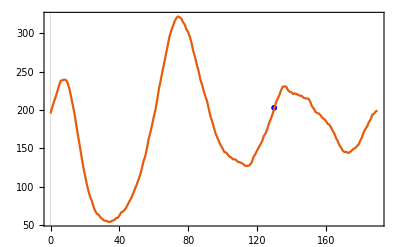

```mathematica
Show[ListPlot[counts[[1]],PlotStyle->Blue,PlotMarkers->{Automatic,Medium}],ListLinePlot[countsSS[[1]]],PlotRange->All]
```

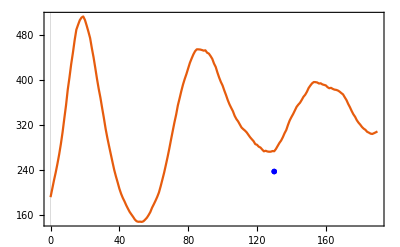

```mathematica
Show[ListPlot[counts[[2]],PlotStyle->Blue,PlotMarkers->{Automatic,Medium}],ListLinePlot[countsSS[[2]]],PlotRange->All]
```

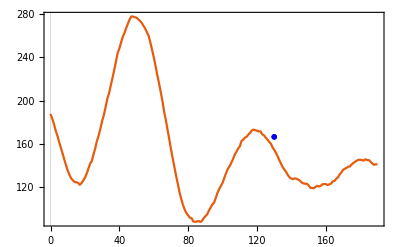

```mathematica
Show[ListPlot[counts[[3]],PlotStyle->Blue,PlotMarkers->{Automatic,Medium}],ListLinePlot[countsSS[[3]]],PlotRange->All]
```